# Model with traditional replication assumptions

```mathematica
ClearAll["Global`*"];


(*set working directory that plots will go into*)

SetDirectory["\\Users\\jabunce\\Dropbox\\Matsigenka-Mestizo_project_2014\\perception_analysis\\xcult_dynamics"];
(*
SetDirectory["/Users/johnbunce/Dropbox/Matsigenka-Mestizo_project_2014/perception_analysis/xcult_dynamics"];
*)


(*Note that A and B in the following equations are the same as Groups S and L, respectively, in the text*)
```

## Functions

```mathematica
(*****************logistic function - increasing*************)
Logistic[x_]:=Module[{},1/(1+Exp[-1*x])];


(*****************Function to simulate phenotype evolution****************)
xcultsim[
matAinit_,(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit_,(*(matrix) initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)
tmax_,(*# sims*)
b_,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c_,(*cost of coordinating using norm that is not personally held*)
a_,(*(vector) probability of assorting to interact with members of your own group, rather than with outgroup {aA,aB}*)
m_,(*cost of having to learn and maintain cross-cultural competence*)
i_,(*identity pride: independent payoff for personally-holding norm that others know*)
muA_(*effect of a power difference on copying between groups*)
]:=Module[{},

(*intialize vectors and matrices*)
matA=matAinit;(*matrix of phenotypes in each group*)
matB=matBinit;
matAall=matAinit;(*list holding matrices of all phenotype freqs for group A over time*)
matBall=matBinit;
fitAtilde={{1,1},{1,1}};(*anticipated fitness of phenotypes in group A: {{A11,A1c},{A2c,A22}}*)
fitBtilde={{1,1},{1,1}};
fitAalltilde=fitAtilde;(*matrix holding all anticipated phenotype fitnesses for group A over time*)
fitBalltilde=fitBtilde;



(*simulation*)
For[t=1,t<=tmax,t++,


Clear[pA11,pA1X,pA2X,pA22,
pB11,pB1X,pB2X,pB22,
bA,bB,
wA11,wA1X,wA2X,wA22,
wB11,wB1X,wB2X,wB22,
wA11temp,wA1Xtemp,wA2Xtemp,wA22temp,
wB11temp,wB1Xtemp,wB2Xtemp,wB22temp,
wA11tildetemp,wA1Xtildetemp,wA2Xtildetemp,wA22tildetemp,
wB11tildetemp,wB1Xtildetemp,wB2Xtildetemp,wB22tildetemp,
poA1,poB1,
pAtildetot,pBtildetot];


(*phenotype payoffs*)

wA11temp=aA*(pA11+pA1X+pA2X)+(1-aA)*(pB11+pB1X+pB2X)*(1+bA)+
i*(pA11+pA1X)*(pB2X+pB22)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA1Xtemp=aA*(pA11+pA1X+pA2X*(1-c/2)+pA22*(1-c))+
(1-aA)*(pB11+pB1X*(1+bA)+pB2X*(1+bA-c/2)+pB22*(1+bA-c))
-m+i*(pA11+pA1X)*(pB2X+pB22)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA2Xtemp=aA*(pA11*(1-c)+pA1X*(1-c/2)+pA2X+pA22)+
(1-aA)*(pB11*(1+bA-c)+pB1X*(1+bA-c/2)+pB2X*(1+bA)+pB22*(1+bA))
-m+i*(pA2X+pA22)*(pB11+pB1X)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA22temp=aA*(pA1X+pA2X+pA22)+(1-aA)*(pB1X+pB2X+pB22)*(1+bA)+
i*(pA2X+pA22)*(pB11+pB1X)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};



wB11temp=aB*(pB11+pB1X+pB2X)+(1-aB)*(pA11+pA1X+pA2X)*(1+bB)+
i*(pB11+pB1X)*(pA2X+pA22)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB1Xtemp=aB*(pB11+pB1X+pB2X*(1-c/2)+pB22*(1-c))+
(1-aB)*(pA11*(1+bB)+pA1X*(1+bB)+pA2X*(1+bB-c/2)+pA22*(1+bB-c))
-m+i*(pB11+pB1X)*(pA2X+pA22)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB2Xtemp=aB*(pB11*(1-c)+pB1X*(1-c/2)+pB2X+pB22)+
(1-aB)*(pA11*(1+bB-c)+pA1X*(1+bB-c/2)+pA2X*(1+bB)+pA22*(1+bB))
-m+i*(pB2X+pB22)*(pA11+pA1X)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB22temp=aB*(pB1X+pB2X+pB22)+(1-aB)*(pA1X+pA2X+pA22)*(1+bB)+
i*(pB2X+pB22)*(pA11+pA1X)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};


(*new phenotype frequencies after updating*)

pA11prime=pA11*(pA11+pA1X*Logistic[(muA*(wA11-wA1X))]+
pA2X*Logistic[(muA*(wA11-wA2X))]+
pA22*Logistic[(muA*(wA11-wA22))])//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11-> wA11temp,
wA1X-> wA1Xtemp,
wA2X-> wA2Xtemp,
wA22-> wA22temp,
wB11-> wB11temp,
wB1X-> wB1Xtemp,
wB2X-> wB2Xtemp,
wB22-> wB22temp
};

pA1Xprime=pA11*pA1X*Logistic[(muA*(wA1X-wA11))]+
pA1X*(pA11+pA1X)+
pA1X*pA2X*(1/2*1+1/2*Logistic[(muA*(wA1X-wA2X))])+
pA1X*pA22*Logistic[(muA*(wA1X-wA22))]+
pA2X*pA11*Logistic[(muA*(wA11-wA2X))]+
pA2X*pA1X*(1/2*0+1/2*Logistic[(muA*(wA1X-wA2X))])+ 
pA22*pA11*Logistic[(muA*(wA11-wA22))]+
pA22*pA1X*Logistic[(muA*(wA1X-wA22))]//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11-> wA11temp,
wA1X-> wA1Xtemp,
wA2X-> wA2Xtemp,
wA22-> wA22temp,
wB11-> wB11temp,
wB1X-> wB1Xtemp,
wB2X-> wB2Xtemp,
wB22-> wB22temp
};


pA22prime=pA22*(pA22+pA2X*Logistic[(muA*(wA22-wA2X))]+
pA1X*Logistic[(muA*(wA22-wA1X))]+
pA11*Logistic[(muA*(wA22-wA11))])//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11-> wA11temp,
wA1X-> wA1Xtemp,
wA2X-> wA2Xtemp,
wA22-> wA22temp,
wB11-> wB11temp,
wB1X-> wB1Xtemp,
wB2X-> wB2Xtemp,
wB22-> wB22temp
};

pA2Xprime=1-pA11prime-pA1Xprime-pA22prime;




pB22prime=pB22*(pB22+pB2X*Logistic[(muA*(wB22-wB2X))]+
pB1X*Logistic[(muA*(wB22-wB1X))]+
pB11*Logistic[(muA*(wB22-wB11))])//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11-> wA11temp,
wA1X-> wA1Xtemp,
wA2X-> wA2Xtemp,
wA22-> wA22temp,
wB11-> wB11temp,
wB1X-> wB1Xtemp,
wB2X-> wB2Xtemp,
wB22-> wB22temp
};

pB1Xprime=pB11*pB1X*Logistic[(muA*(wB1X-wB11))]+
pB1X*(pB11+pB1X)+
pB1X*pB2X*(1/2*1+1/2*Logistic[(muA*(wB1X-wB2X))])+
pB1X*pB22*Logistic[(muA*(wB1X-wB22))]+
pB2X*pB11*Logistic[(muA*(wB11-wB2X))]+
pB2X*pB1X*(1/2*0+1/2*Logistic[(muA*(wB1X-wB2X))])+ 
pB22*pB11*Logistic[(muA*(wB11-wB22))]+
pB22*pB1X*Logistic[(muA*(wB1X-wB22))]//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11-> wA11temp,
wA1X-> wA1Xtemp,
wA2X-> wA2Xtemp,
wA22-> wA22temp,
wB11-> wB11temp,
wB1X-> wB1Xtemp,
wB2X-> wB2Xtemp,
wB22-> wB22temp
};


pB11prime=pB11*(pB11+pB1X*Logistic[(muA*(wB11-wB1X))]+
pB2X*Logistic[(muA*(wB11-wB2X))]+
pB22*Logistic[(muA*(wB11-wB22))])//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11-> wA11temp,
wA1X-> wA1Xtemp,
wA2X-> wA2Xtemp,
wA22-> wA22temp,
wB11-> wB11temp,
wB1X-> wB1Xtemp,
wB2X-> wB2Xtemp,
wB22-> wB22temp
};

pB2Xprime=1-pB22prime-pB1Xprime-pB11prime;


(*update phenotype and fitness matrices*)
digs=300;

matA = N[{{pA11prime,pA1Xprime},{pA2Xprime,pA22prime}},digs];
matB = N[{{pB11prime,pB1Xprime},{pB2Xprime,pB22prime}},digs];
fitAtilde=N[{{wA11tildetemp,wA1Xtildetemp},{wA2Xtildetemp,wA22tildetemp}},digs];
fitBtilde=N[{{wB11tildetemp,wB1Xtildetemp},{wB2Xtildetemp,wB22tildetemp}},digs];

(*accumulate phenotype freqs and fitnesses across sims*)
matAall=Join[matAall,matA];
matBall=Join[matBall,matB];
fitAalltilde=Join[fitAalltilde, fitAtilde];
fitBalltilde=Join[fitBalltilde, fitBtilde]


];(*for t*)

];(*xcultsim*)
```

## Simulation trajectories

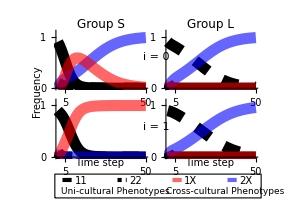

./figures/FigureTrajAtrad.pdf

```mathematica
(*Phenotype frequency trajectories*)

(*matching pheno freqs: all machis and mestizos, grouping into uni-cult comp*)

(*A*********************************************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=5/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity pride: independent payoff for personally-holding norm that others know*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


figaA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figaB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{White,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*B******************** increase i ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=5/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figbA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{50,"50"},{5,"5"}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figbB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{White,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];

(***************************** assemble plots into Figure ****************************)
FigureTrajAtrad=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[1.5]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Rotate[Style["Frequency",10],90Degree],{30,-231}],
(*Inset[Rotate[Style["Frequency",10],90Degree],{20,-342}],*)
Inset[Style["Time step",10],{235,-462}],
Inset[Style["Time step",10],{595,-462}],
Inset[Row[{Style["i",Italic,10],Style[" = 0",10]}],{380,-120},{Left,Center}],
Inset[Row[{Style["i",Italic,10],Style[" = 1",10]}],{380,-345},{Left,Center}],

x1=-85;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{175+x1,-78+y1},{850+x1,-155+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural Phenotypes",9],{195+x1,-135+y1},{Left,Center}],
Inset[Style["22",10],{440+x1,-100+y1}],
Inset[Style["1X",10],{620+x1,-100+y1}],
Inset[Style["Cross-cultural Phenotypes",9],{540+x1,-135+y1},{Left,Center}],
Inset[Style["2X",10],{800+x1,-100+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{380+x1,-97+y1},{410+x1,-97+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{560+x1,-97+y1},{590+x1,-97+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{740+x1,-97+y1},{770+x1,-97+y1}}]}
},
ImageSize->300
],(*Graphics Grid*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)

Export["./figures/FigureTrajAtrad.pdf",FigureTrajAtrad,"PDF"]
```

## Trajectory Sensitivity

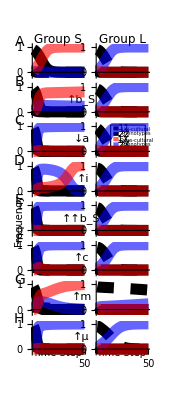

./figures/FigureTrajAlltrad.pdf

```mathematica
(*trajectory sensitivity analysis*)

(*A******************** no power differences *************************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={0,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


figaA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{5,""},{50,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figaB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*B******************** power difference ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figbA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figbB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];




(*C******************** low affinity ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figcA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figcB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*D******************** identity ***********************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figdA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figdB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*E******************** large power difference ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={8,1},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figeA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figeB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*F******************** high cognitive dissonance ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=9/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figfA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figfB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*G******************** high maintenance ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figgA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figgB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*H******************** high payoff bias ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=3 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

fighA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,"50"},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

fighB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(****************** assemble plots into Figure ****************************)
FigureTrajAlltrad=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB},{figcA,figcB},{figdA,figdB},
{figeA,figeB},{figfA,figfB},{figgA,figgB},{fighA,fighB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Style["A",14],{20,-30}],
Inset[Style["B",14],{20,-253}],
Inset[Style["C",14],{20,-476}],
Inset[Style["D",14],{20,-699}],
Inset[Style["E",14],{20,-922}],
Inset[Style["F",14],{20,-1145}],
Inset[Style["G",14],{20,-1368}],
Inset[Style["H",14],{20,-1591}],
Inset[Rotate[Style["Frequency",10],90Degree],{20,-1032}],
Inset[Style["Time Step",10],{235,-1782}],
Inset[Style["Time Step",10],{595,-1782}],

Inset[Style[UpArrow["",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{370,-353}],
Inset[Style[DownArrow["",Style["a",Italic,10]]],{370,-576}],
Inset[Style[UpArrow["",Style["i",Italic,10]]],{380,-799}],
Inset[Style[UpArrow["","",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{370,-1022}],
Inset[Style[UpArrow["",Style["c",Italic,10]]],{370,-1245}],
Inset[Style[UpArrow["",Style["m",Italic,10]]],{370,-1468}],
Inset[Style[UpArrow["",Style["μ",10]]],{370,-1691}], (*type \[Mu ] w/o the space*)

x1=350;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{185+x1,-78+y1},{380+x1,-210+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural",5],{330+x1,-105+y1}],
Inset[Style["Phenotypes",5],{330+x1,-125+y1}],
Inset[Style["22",10],{260+x1,-130+y1}],
Inset[Style["1X",10],{260+x1,-160+y1}],
Inset[Style["Cross-cultural",5],{330+x1,-165+y1}],
Inset[Style["Phenotypes",5],{330+x1,-185+y1}],
Inset[Style["2X",10],{260+x1,-190+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{200+x1,-127+y1},{230+x1,-127+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{200+x1,-157+y1},{230+x1,-157+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{200+x1,-187+y1},{230+x1,-187+y1}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)

Export["./figures/FigureTrajAlltrad.pdf",FigureTrajAlltrad,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

## Long - run sensitivity

Done part a

Done part b

Done part c

Done part d

Done part e

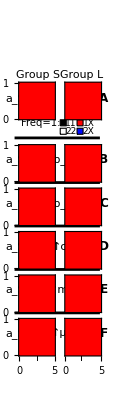

./figures/AllDenstrad.pdf

```mathematica
(*Long-run trends sensitivity analysis*)

Clear[pA11,pA1X,pA2X,pA22,pB11,pB1X,pB2X,pB22,sA,b,c,a,m,i,muW,muB,bA,bB,wA11,wA1X,wA2X,wA22,wB11,wB1X,wB2X,wB22, matA, matB, matAall, matBall,fitA, fitB, fitAall, fitBall,A1Xmat,A2Xmat,B1Xmat,B2Xmat];


aASeq=Range[0,1,1/20];(*in-group affinity sequence*)
aBSeq=1-((1-aASeq)*1/2); (* keep group B twice as big as group A *)
iSeq=Range[0,5,1/4]; (*i sequence*)
tmaxAll =100; (*# sims, change this to something like 20 and it will run much faster*)
pgAinitAll={{9/10,0},{0,1/10}}; (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
pgBinitAll={{1/10,0},{0,9/10}};

(*A******** no power difference ****************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={0,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
(*Round[grpAimat,0.01] //MatrixForm;*)

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

(*
Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;
*)

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) , (*Blue*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

a1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

a2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part a"]


(*B********** low power difference ***********************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
(*Round[grpAimat,0.01] //MatrixForm;*)

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

(*
Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;
*)

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

b1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

b2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part b"]


(*C******* high power difference ****************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={8,1},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
(*Round[grpAimat,0.01] //MatrixForm;*)

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

(*
Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;
*)

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

c1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

c2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part c"];



(*D********* high c *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=9/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
(*Round[grpAimat,0.01] //MatrixForm;*)

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

(*
Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;
*)

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

d1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

d2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part d"];


(*E*********  high m *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
(*Round[grpAimat,0.01] //MatrixForm;*)

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

(*
Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;
*)

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

e1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

e2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part e"];



(*F********* high mu *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={4,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=3 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
(*Round[grpAimat,0.01] //MatrixForm;*)

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

(*
Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;
*)

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

f1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

f2=Show[B11plot,B2Xplot,B1Xplot];



(*assemble plots into Fig 2*)
moveright=30;
moveup=10;

AllDenstrad=Panel[
GraphicsGrid[
{{"",""},{a1,a2},{b1,b2},{c1,c2},{d1,d2},{e1,e2},{f1,f2}},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0.2], (*horizontal space before, between, after plots*)
Scaled[0.1],
Scaled[0.4]
},
{
Scaled[0], (*vertical space above, between, below plots*)
Scaled[0],
Scaled[0.5], (*was 0.3*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.2]}
},
Frame->True,
FrameStyle->Directive[White, Opacity[0]],
Epilog->{
Inset[Style["A",12,Bold],{770,-510}],
Inset[Style["B",12,Bold],{770,-1020}],
Inset[Style["C",12,Bold],{770,-1380}],
Inset[Style["D",12,Bold],{770,-1740}],
Inset[Style["E",12,Bold],{770,-2100}],
Inset[Style["F",12,Bold],{770,-2460}],

Inset[Style[UpArrow["",Subscript[Style["b",Italic,6],Style["S",Italic,4]]]],{400,-1020}],
Inset[Style[DoubleUpArrow["",Subscript[Style["b",Italic,6],Style["S",Italic,4]]]],{400,-1380}],
Inset[Style[UpArrow["",Style["c",Italic,6]]],{400,-1740}],
Inset[Style[UpArrow["",Style["m",Italic,6]]],{400,-2100}],
Inset[Style[UpArrow["",Style["μ",6]]],{400,-2460}], (*type \[Mu ] w/o the space*)

Inset[Style["Group S",11],{225,-315}],
Inset[Style["Group L",11],{590,-315}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-510}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1020}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1380}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1740}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-2100}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-2460}],
Inset[Style["i",Italic,10],{220,-2660}],
Inset[Style["i",Italic,10],{590,-2660}],

Inset[Style["Freq=1:",10],{250,-720}],
{EdgeForm[Thin],Black,Rectangle[{440-moveright,-740},{490-moveright,-690}]}, (*{xmin,ymin},{xmax,ymax}*)
Inset[Style["11",9],{530-moveright,-720}],
{EdgeForm[Thin],Hue[1,1,1,1],Rectangle[{580-moveright,-740},{630-moveright,-690}]},
Inset[Style["1X",9],{675-moveright,-720}],

Inset[Style["",10],{250,-780}],
{EdgeForm[Thin],White,Rectangle[{440-moveright,-810},{490-moveright,-760}]},
Inset[Style["22",9],{530-moveright,-790}],
{EdgeForm[Thin],Hue[3.3/5,1,1,1],Rectangle[{580-moveright,-810},{630-moveright,-760}]},
Inset[Style["2X",9],{675-moveright,-790}],

{AbsoluteThickness[2],Black,Line[{{30,-840},{740,-840}}]}, 
{AbsoluteThickness[2],Black,Line[{{30,-1210},{740,-1210}}]}, 
{AbsoluteThickness[2],Black,Line[{{30,-1570},{740,-1570}}]},
{AbsoluteThickness[2],Black,Line[{{30,-1930},{740,-1930}}]},
{AbsoluteThickness[2],Black,Line[{{30,-2290},{740,-2290}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,0}}
](*panel*)

Export["./figures/AllDenstrad.pdf",AllDenstrad,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```